# 1. Solving the Gross - Pitaevskii equation in Mathematica

## Jacques Tempere, September 2022 TQC, Dept. Fysica, Universiteit Antwerpen

In this notebook I explain how to simulate the 1D Gross - Pitaevskii equation,

ⅈ ℏ d/dtψ(x,t) = ℏ^2/(2m)d^2/dx^2ψ(x,t) + V(x,t) ψ(x,t) + g |ψ(x,t)|^2ψ(x,t) .

This equation describes the time evolution of an interacting atomic Bose-Einstein condensate in a time-dependent external potential. More background on Bose-Einstein condensates and the Gross-Pitaevskii equation can be found, for example, in the following books:

"Bose–Einstein Condensation in Dilute Gases, 2nd ed.", C.J. Pethick and H. Smith, Cambridge University Press (2011),  
"Bose-Einstein condensation", L. Pitaevskii and S. Stringari, Clarendon / Oxford University Press (2003).

A study of the split-step method that I implement in this notebook can be found in:

“Split-step Fourier methods for the Gross-Pitaevskii equation”, J. Javanainen and J. Ruostekoski, J. Phys. A: Math. Gen. 39, L179 (2006); link to preprint on arXiv.

## System parameters and setup

### Spatial grid

We use units ℏ = m = ξ = 1 where ξ is the healing length of the condensate.

First, there are some system parameters to set (you can of course change them). The length of the box L, and the number of spatial points determine the step size Δx in real space:

```mathematica
L=50.;
npoints=2^9;
Δx=L/npoints;
```

This step size should be smaller than the healing length, so smaller than 1 in our units. Around 0.1 is often fine, but it is always good to test the results by doing a run with a finer grid and seeing that it all works out fine. The number of points is chosen as a power of 2 in order to speed up the fast fourier transform that we will need later.

I prefer setting the origin of my x - axis in the middle of the box, so x runs from - L/2 to + L/2 . Note that we use discrete Fourier transforms, and thus implicitly assume the point at +L/2 is equivalent to the point at -L/2 and is not included in “xgrid”, the list of spatial coordinates of the distinct positions in our simulation:

```mathematica
xgrid=Table[ (j-1) Δx-L/2, {j,1,npoints}];
```

### Number of atoms (and interaction strength)

Having set the size of the box and fixed the grid, it also matters how many atoms we put into the box, which determines the average density n. However, our units already fix the chemical potential μ, because of the following relations:

μ = m c^2 = g n =ℏ^2/(m ξ^2)=1

In fact, these are just different ways to write down the characteristic energy scale of the system. Here, c is the sound velocity in the condensate (c = 1 in our units), and g is the interaction strength. In 3D it is related to the s-wave scattering length a_s by g = 4π ℏ^2 a_s/m . If the condensate is confined to 1D by a strong harmonic confinement with frequency ω_⊥ then g = 2 ℏ ω_⊥ a_s .

For the Gross-Pitaevskii equation to be valid (i.e. the effect of quantum fluctuations in each grid point to be negligible), the number of atoms per grid point should be much larger than one. Let's make it ten times as large:

```mathematica
Natoms=10*npoints
```

5120

Five thousand atoms is not too unrealistic to put in a 1D (cigar-shaped trap). By our choice of units, we have fixed the interaction strength already, and in accordance the formula above it is:

```mathematica
g = L/Natoms
```

0.00976563

Make sure this always stays much smaller than one! If you have too strong interactions (or a too low condensate density) the Gross-Pitaevskii equation no longer gives a correct description of the system.

### Time step

Next we still need to set the size of the time step. This should be shorter than the characteristic time than can be constructed from  the energy and the spatial grid size, t_char=(m Δx^2)/ℏ, or in out units simply Δx^2. It should also be shorter than the time needed for sound to cross one grid step, t_snd=Δx/c, or simply Δx in our units. But, since Δx is already chosen less than one,  t_char < t_snd and t_char gives the most stringent restriction. Here, we’ll take out time scale ten times smaller than this characteristic time.

```mathematica
Δt = 0.1 Δx^2
```

0.000957411

### Box potential

We use a box potential with relatively sharp edges, and a height of 5 μ.

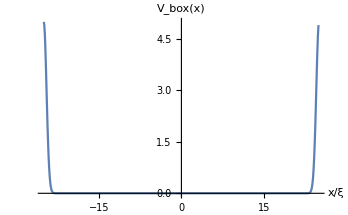

```mathematica
Vbox=5Chop[Table[ Exp[-2.(x-L/2.)^2]+Exp[-2.(x+L/2.)^2], {x,xgrid}]];
ListPlot[ Transpose[{xgrid,Vbox}], PlotRange->All, Joined->True, AxesLabel->{"x/ξ","V_box(x)"}]
```

A  first guess for the wave function could then be

```mathematica
ψ0=√(Natoms/L) Table[ -Tanh[0.25(x-L/2.)]*Tanh[0.25(x+L/2.)], {x,xgrid}];
```

The norm of this wave function is not precisely the number of atoms. Integrating over space using the trapezoid rule we find somewhat less than 5120 atoms.

```mathematica
norm0=Total[ Table[ (Abs[ψ0[[j]]]^2+Abs[ψ0[[j+1]]]^2)/2  Δx, {j,1,npoints-1}]]
```

4915.15

Normalized to the square root of the number of atoms, this is

```mathematica
ψguess=√(Natoms/norm0)ψ0;
```

```mathematica
Total[ Table[ (Abs[ψguess[[j]]]^2+Abs[ψguess[[j+1]]]^2)/2  Δx, {j,1,npoints-1}]]
```

5120.

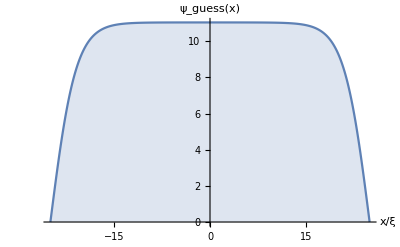

```mathematica
ListPlot[ Join[ Transpose[ {xgrid, ψguess} ],{{L/2,First[ψguess]}}] (*periodicity*), AxesLabel->{"x/ξ","ψ_guess(x)"}, Joined->True, Filling->Bottom]
```

Actually, our guess is not that good; we' ve overestimated the healing length for the condensate to get back to its bulk value. We’ll use this example, though, to see how the Gross-Pitaevskii equation can be used to relax this guess to the ground state of the system.

### Reciprocal space grid and more subtleties of the Fourier function

We' ll use Mathematica’s built-in “Fourier” and “InverseFourier” functions. However, there is a subtlety: we would also like to get a k-space grid that goes from -π/Δx to +π/Δx in steps of 2π/L (and again, due to periodicity it will not include this last point, assuming the value is equal to the first), i.e. the first “Brillouin zone” of our periodic system.

```mathematica
kgrid=Table[ (j-1) (2 π)/L-π/Δx, {j,1,npoints}];
```

```mathematica
Length[kgrid]
```

512

For example, let' s take a function that is a gaussian around 10, with with 5 in our box of size 50. We code it as a list of “npoints” values,

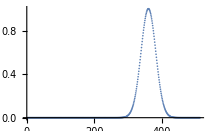

```mathematica
ψtest=Table[ Exp[-((xpos-10)/3)^2]  , {xpos,xgrid} ]; ListPlot[ψtest, PlotRange->All]
```

```mathematica
Length[ψtest]
```

512

If you want the x-axis to represent spatial position then use

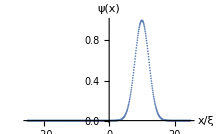

```mathematica
ListPlot[ Transpose[{xgrid,ψtest}], PlotRange->All, AxesLabel->{"x/ξ", "ψ(x)"}]
```

Now, here' s what Fourier does :

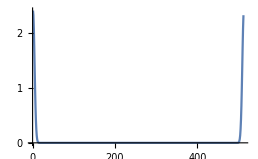

```mathematica
ψktest=Fourier[ ψtest ]; 
ListPlot[ Map[Abs,ψktest], PlotRange->All ,Joined->True ]
```

The shift to position 10 is encoded in the phase of the fourier transform, but its absolute value should still be a gaussian centered around wavenumber zero (and narrower as the original one gets broader) The reason for the weird shape above is that the function Fourier maps onto the domain [0, 2π/Δx] rather than [-π/Δx, +π/Δx]. We need to shift the whole thing by half a Brillouin zone:

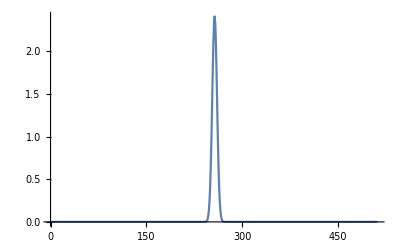

```mathematica
ψktest2=RotateRight[ψktest,npoints/2];
ListPlot[ Map[Abs,ψktest2], PlotRange->All ,Joined->True ]
```

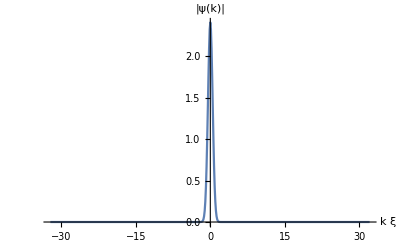

```mathematica
ListPlot[ Transpose[{kgrid, Map[Abs,ψktest2]}], PlotRange->All ,Joined->True, AxesLabel->{"k ξ", "|ψ(k)|"} ]
```

Now it is indeed centered around k=0. To do the inverse Fourier transform, we' ll first need to undo the backwards!

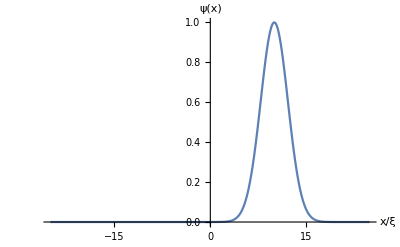

```mathematica
ψrecover=InverseFourier[ RotateLeft[ψktest2,npoints/2] ];
ListPlot[ Transpose[{xgrid,ψrecover}], PlotRange->All, AxesLabel->{"x/ξ", "ψ(x)"}, Joined->True]
```

Let’s now test this out for our guess in the box potential:

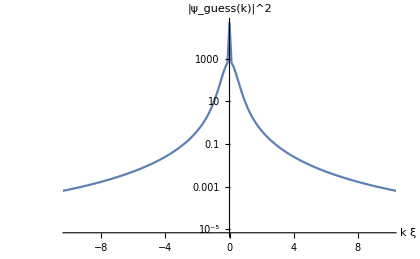

```mathematica
ListLogPlot[ Transpose[{kgrid, Map[ (Abs[#]^2)&,  RotateRight[Fourier[ ψguess ],npoints/2]]}] , 
Joined->True, PlotRange->{{-10,10},All}, AxesLabel->{"k ξ", "|ψ_guess(k)|^2"} ]
```

If we' d just had a flat wave function, we’d get a delta peak at k=0. Now we still get a very sharp peak (a single value) at k=0, indeed representing that the majority of the atoms are all in the k=0 state. The features at the edge of the box results in the wings.

## The split - step method: introduction

Each time step consists of a unitary transformation exp{-ⅈ H Δt} on the condensate wave function, generated by the Gross-Pitaevskii Hamiltonian H. For small time steps, the Lee-Trotter formula allows to split the evolution in a kinetic energy unitary and a potential energy unitary. The kinetic step is most easily performed in momentum space, while the potential step is most easily performed in real space. That’s why a fourier transform is used between every step to go from position to momentum representation. In summary, what we want to do is:

ψ_old(x)⟶_FT  ψ(k)  ⟶_kin  ψ(k)Exp[-ⅈ(ℏk)^2/(2m)Δt]  ⟶_(FT^-1)  ψ̄(x)  ⟶_pot  ψ̄(x)Exp[-ⅈ(V+g|ψ̄|^2)Δt]=ψ_new(x)

When working with complex pre-factors in the time derivative part of the Gross - Pitaevskii equation (to find the ground state introduce a bit of dissipation), it will be necessary to renormalize the wave function at every step as we discuss below.

```mathematica
ψold=ψguess;
```

Here' s what one step would look like, starting from ψold. The kinetic part of the unitary time evolution is the same in every step and can be stored in a list

```mathematica
kinU=Table[ Exp[-ⅈ k^2/2 Δt], {k,kgrid}]   (*construct kinetic time evol operator*);
```

The potential part of the unitary evolution will have to be computed at every timestep, since it depends on the wave function

```mathematica
potU=MapThread[ Exp[-ⅈ (#1 + g Abs[#2]^2-1.)Δt]&, {Vbox,ψold} ]  (*construct potential time evol operator*) ;
```

The -1. as the last term between round brackets is actually -μ, the chemical potential term. Here I’ve replaced μ by its value in our units, namely 1. Then the time step evolution for the wave function is performed through

```mathematica
ψFTold=RotateRight[Fourier[ ψold ],npoints/2]   (*to reciprocal space*) ;
ψFTnew=MapThread[ Times, {kinU,ψFTold}]   (*kinetic part of the time evolution*);
ψinterim=InverseFourier[RotateLeft[ ψFTnew, npoints/2]]   (*back to real space*);
ψnew= MapThread[ Times,{potU,ψinterim} ]   (*potential part of the time evolution*);
```

This, along with the calculation of potU is what we should put in a loop to get the time evolution. However, the pure time evolution is unitary, the condensate is incapable of evolving to its ground state. To allow for a relaxation, we have to use imaginary-time evolution.

## Imaginary-time evolution

We basically have the same algorithm as before, but now we replace ⅈ Δt by Δt. This will turn the time evolution operator into exp[-β H], the density matrix, and by letting the imaginary time “β” run large, we bring the system to colder effective temperatures and pluck out the ground state. However, in each step, we must normalize the wave function again. So, let’s see what we get:

```mathematica
kinUim=Table[ Exp[-k^2/2 Δt], {k,kgrid}]   (*construct kinetic operator*);
ψold=ψguess;
Do[
potUim=MapThread[ Exp[-(#1 + g Abs[#2]^2-1.)Δt]&, {Vbox,ψold} ];
ψFTold=RotateRight[Fourier[ ψold ],npoints/2]   (*to reciprocal space*) ;
ψFTnew=MapThread[ Times, {kinUim,ψFTold}]   (*kinetic part of the time evolution*);
ψinterim=InverseFourier[RotateLeft[ ψFTnew, npoints/2]]   (*back to real space*);
ψnew= MapThread[ Times,{potUim,ψinterim} ]   (*potential part of the time evolution*);
norm=Total[ Table[ (Abs[ψnew[[j]]]^2+Abs[ψnew[[j+1]]]^2)/2  Δx, {j,1,npoints-1}]];
ψold=√(Natoms/norm)ψnew,
{timestep,1,2000}] //Timing
```

{3.28125,Null}

```mathematica
ψground=ψold;
```

The code above relaxes our initial guess for the wave function in the box to the ground state . The result is shown in the figure below:

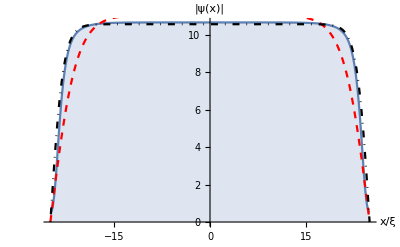

```mathematica
Show[
ListPlot[ Join[ Transpose[ {xgrid, Abs[ψground]} ],{{L/2,Abs[First[ψground]]}}] , AxesLabel->{"x/ξ","|ψ(x)|"}, Joined->True, Filling->Bottom, PlotRange->All],
ListPlot[ Join[ Transpose[ {xgrid, Abs[ψguess]} ],{{L/2,Abs[First[ψguess]]}}], Joined->True,PlotStyle->{Dashed,Red}],
ListPlot[ Join[ Transpose[ {xgrid, Abs[ψbetterguess]} ],{{L/2,Abs[First[ψguess]]}}], Joined->True,PlotStyle->{DotDashed,Black}]]
```

The condensate is indeed doing what we expect. The original guess (red dashed) was staying away too far from the walls. The time evolution lets the condensate approach the walls to the correct distance.  After 2000 timesteps (executed in under 3 seconds) we are already quite close to the next best guess, shown as a black dash-dotted line and given here below:

```mathematica
ψ0=√(Natoms/L) Table[ -Tanh[(x-L/2.)/√2]*Tanh[(x+L/2.)/√2], {x,xgrid}];
```

```mathematica
norm0=Total[ Table[ (Abs[ψ0[[j]]]^2+Abs[ψ0[[j+1]]]^2)/2  Δx, {j,1,npoints-1}]]
```

4710.39

```mathematica
ψbetterguess=√(Natoms/norm0)ψ0;
```

Note that if you start with a purely real guess (a good assumption for a Bose ground state), then the imaginary time evolution will keep your wave function purely real, up to numerical precision.

## Real time evolution

Once we’ve found a good initial state to start with (usually the ground state of an appropriately prepared condensate), we can now add a perturbation potential and see how the condensate wave function evolves. To keep a little bit of dissipation on, we’re going to replace ⅈ Δt by (ⅈ + 0.01)Δt . So, we’re not working purely in imaginary time, but we allow for a little bit of damping. Of course, we’ll need to renormalize, otherwise we just lose atoms.

The perturbation can be time dependent, and in general it is a good idea to switch in on slowly, on a scale compared to the characteristic time scale t_char . But here, we’re going to look what happens for a sudden change: a perturbation potential given by

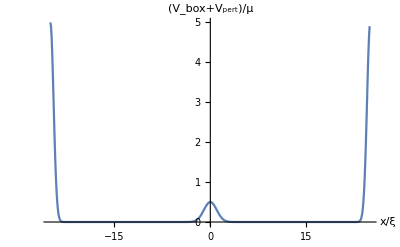

```mathematica
Vpert=0.5 Chop[Table[ Exp[-0.5 x^2], {x,xgrid}]];
ListPlot[ Transpose[{xgrid,Vbox+Vpert}], PlotRange->All, Joined->True, AxesLabel->{"x/ξ","(V_box+V_pert)/μ"}]
```

is suddenly switched on. For the split-step method, this potential simply gets added to Vbox in the potential energy unitary evolution step. We’ll take a snapshot of the condensate every 500 timesteps.

```mathematica
kinU=Table[ Exp[-(ⅈ+0.005)k^2/2 Δt], {k,kgrid}]   (*construct kinetic operator*);
snapshots={ψground};
ψold=ψground;
Do[
potU=MapThread[ Exp[-(ⅈ+0.005)(#1 + g Abs[#2]^2/2-1.)Δt]&, {Vbox+Vpert,ψold} ];
ψFTold=RotateRight[Fourier[ ψold ],npoints/2]   (*to reciprocal space*) ;
ψFTnew=MapThread[ Times, {kinU,ψFTold}]   (*kinetic part of the time evolution*);
ψinterim=InverseFourier[RotateLeft[ ψFTnew, npoints/2]]   (*back to real space*);
ψnew= MapThread[ Times,{potU,ψinterim} ]   (*potential part of the time evolution*);
norm=Total[ Table[ (Abs[ψnew[[j]]]^2+Abs[ψnew[[j+1]]]^2)/2  Δx, {j,1,npoints-1}]];
ψold=√(Natoms/norm)ψnew;
If[ Mod[timestep,250]==0, AppendTo[snapshots,ψold]],
{timestep,1,10000}] //Timing
```

{20.2188,Null}

```mathematica
Manipulate[ 
ListPlot[ Join[ Transpose[ {xgrid, Abs[ snapshots[[jj]] ]} ],{{L/2,Abs[First[snapshots[[jj]]]]}}] , AxesLabel->{"x/ξ","|ψ(x)|"}, Joined->True, Filling->Bottom, PlotRange->{0,13}],
{jj,1,Length[snapshots],1}]
```

We see the effect of the potential that we turned on: it depletes the condensate and generates a shockwave preceded by a phonon train that propagates to the edge of the condensate.

## Visualizing the wavefunction

Above, I only plotted the amplitude of the wave function, but its phase also holds important information, namely the velocity field is proportional to the gradient of the phase.

To show the phase we can use a color circle, such that red corresponds to phase 0, then along the colors of the rainbow it goes to yellow-green for π/2, blue for π, violet for 3π/2 and then back to red to connect to 0 again.

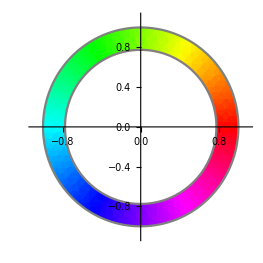

```mathematica
RegionPlot[ (x^2+y^2<1)&&(x^2+y^2>0.6), {x,-1.1,1.1}, {y,-1.1,1.1},
 Axes->True, Frame->False, Ticks->None, 
ColorFunction->Function[{x,y},Hue[ Arg[x+ⅈ y]/(2π) ]], ColorFunctionScaling->False]
```

For example, let' s take the final snapshot in the series from the previous section

```mathematica
wavefunct= Interpolation[  Join[ Transpose[ {xgrid, snapshots[[40]]} ],{{L/2,First[snapshots[[20]]]}}] ]
```

InterpolatingFunction[…]

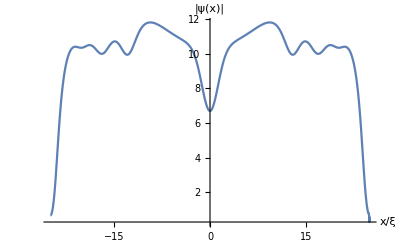

```mathematica
Plot[ Abs[wavefunct[x]],{x,-25,25}, PlotRange->All,AxesLabel->{"x/ξ","|ψ(x)|"}, AxesStyle->Black]
```

Now, we add color representing the phase underneath

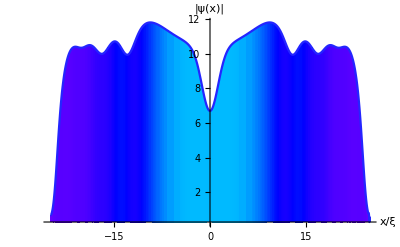

```mathematica
Plot[ Abs[wavefunct[x]],{x,-25,25}, PlotRange->All,AxesLabel->{"x/ξ","|ψ(x)|"}, AxesStyle->Black,
Filling->Bottom,ColorFunction->Function[{x,y},Hue[ Arg[wavefunct[x]]/(2π) ]], ColorFunctionScaling->False]
```

And we can again make a “movie” from it:

```mathematica
Manipulate[ 
wavefunct= Interpolation[  Join[ Transpose[ {xgrid, snapshots[[jj]]} ],{{L/2,First[snapshots[[jj]]]}}] ];
Plot[ Abs[wavefunct[x]],{x,-25,25}, PlotRange->{0,13},AxesLabel->{"x/ξ","|ψ(x)|"}, AxesStyle->Black,Filling->Bottom,ColorFunction->Function[{x,y},Hue[ Arg[wavefunct[x]]/(2π) ]], ColorFunctionScaling->False],
{jj,1,Length[snapshots],1}]
```

The overall absolute value of the phase doesn' t matter physically, the gradients do, as they yield the velocity. So, it can also be useful to plot the velocity separately. Note that as the argument wraps around the 2 π phase circle, sharp outliers can be created.

```mathematica
Manipulate[
velocities=Table[{(xgrid[[nn+1]]+xgrid[[nn]])/2, (Arg[snapshots[[jj,nn+1]]]-Arg[snapshots[[jj,nn]]])/Δx }, {nn,1,npoints-1}];
ListPlot[ velocities, Joined->True, PlotRange->{-0.5,0.5}, AxesLabel->{"x/ξ","v/c"}, AxesStyle->Black],
{jj,1,Length[snapshots],1} ]
```